# Lecture 30: Other Eigenvalue Algorithms Jacobi, Bisection, Divide and Conquer

There are other competitive direct eigen solvers.

```mathematica
m=1500;
AbsoluteTiming[A=RandomReal[{-1,1},{m,m}];]
AbsoluteTiming[{Q,H}=HessenbergDecomposition[A];]
AbsoluteTiming[Eigensystem[A];]
AbsoluteTiming[Eigenvalues[A];]
```

{0.0357175,Null}

{0.536218,Null}

{1.7409,Null}

{1.18887,Null}

```mathematica
m=3000;
AbsoluteTiming[A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;]
AbsoluteTiming[{Q,H}=HessenbergDecomposition[A];]
AbsoluteTiming[Eigensystem[A];]
```

{0.140758,Null}

{5.91001,Null}

{3.77687,Null}

```mathematica
m=3000;
AbsoluteTiming[A=RandomReal[{-1,1},{m,m}];]
AbsoluteTiming[{Q,H}=HessenbergDecomposition[A];]
AbsoluteTiming[Eigensystem[A];]
```

{0.0667524,Null}

{5.81315,Null}

{11.3904,Null}

Real test matrices live on the web. https://math.nist.gov/MatrixMarket/.  Most large matrices are very sparse.

```mathematica
A=Import["https://math.nist.gov/pub/MatrixMarket2/Harwell-Boeing/bcsstruc2/bcsstk17.mtx.gz"]
TabView[{
"A"->MatrixPlot[A],
"A_(1 : SuperscriptBox[10, 3])"->MatrixPlot[A⟦1;;10^3,1;;10^3⟧],
"A_(1 : SuperscriptBox[10, 2])"->MatrixPlot[A⟦1;;10^2,1;;10^2⟧]
}]
```

```mathematica
ListPlot[Eigenvalues[A,100]]
ListPlot[Eigenvalues[A,-100]]
```

```mathematica
AbsoluteTiming[
λs=Eigenvalues[A]
]
```

```mathematica
ListLogPlot[λs]
ListLogPlot[λs⟦-700;;-1⟧,
PlotRange->All]
```

## Hessenberg Decomposition

You just learned a non-iterative algorithm that reduced a general matrix A to an upper Hessenberg matrix H with a sequence of orthogonal similarity transformations i.e. H_0=A and then H_(i+1)=Q_i.H_i.Q_i ᵀ.  Of course, the final H_n has the same eigenvalues as A.   This is the first step in most general dense eigenvalue algorithms. It usually takes about half of the wall clock time.

```mathematica
m=7;
A=RandomReal[{-1,1},{m,m}];
{Q,H}=HessenbergDecomposition[A];
TabView[{
"A"->MatrixPlot[A],
"H"->MatrixPlot[H,ColorRules->{0.0->LightGreen}],
"λ"->TableForm[Map[Eigenvalues,{A,H}]ᵀ]},2]
```

123

The Hessenberg decomposition of a symmetric matrix gives a symmetric Hessenberg matrix.  Remember symmetric real matrices have real eigenvalues.

```mathematica
m=7;
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
{Q,H}=HessenbergDecomposition[A];
TabView[{
"A"->MatrixPlot[A],
"H"->MatrixPlot[H,ColorRules->{0.0->LightGreen}],
"H"->MatrixForm[H],
"λ"->TableForm[Map[Eigenvalues,{A,H}]ᵀ]},2]
```

1234

There are special algorithm to efficiently compute the symmetric tridiagonal matrix T from a symmetric A for this important special case.  There are also special algorithm to efficiently compute the eigenvalues of the symmetric tridiagonal matrix T.  The general purpose algorithm is a main topic of the course.  I am going to explain three more specialized algorithms.  This is lecture 30 in your book.

## Oldest Eigenvalue Algorithm: Jacobi

Before the word “matrix” existed Jacobi needed to compute what would be called the eigenvalues of a real symmetric 7×7 matrix: there were only seven known planets at the time! He invented what is now called the Jacobi method!

This algorithm is still used when high precision small eigenvalues are important. It is also used on some specialized hardware.

#### Background and Code

We can diagonalize a symmetric 2 by 2 matrix using the Givens rotation (p1 | p2
-p2 | p1).   Lets work out the recipe!

```mathematica
AHat=({{p1, p2}, {-p2, p1}}).({{a11, a12}, {a12, a22}}).({{p1, -p2}, {p2, p1}});
MatrixForm[AHat]
```

(p1 (a11 p1+a12 p2)+p2 (a12 p1+a22 p2) | -p2 (a11 p1+a12 p2)+p1 (a12 p1+a22 p2)
p1 (a12 p1-a11 p2)+p2 (a22 p1-a12 p2) | -p2 (a12 p1-a11 p2)+p1 (a22 p1-a12 p2))

There are two values of p1 that work! Of course, we need to check that the expression under the square root is not negative if we want a real computation.

```mathematica
Solve[AHat⟦1,2⟧==0,p1]
```

{{p1→(a11 p2-a22 p2-√(a11^2+4 a12^2-2 a11 a22+a22^2) p2)/(2 a12)},{p1→(a11 p2-a22 p2+√(a11^2+4 a12^2-2 a11 a22+a22^2) p2)/(2 a12)}}

It is OK since a11^2+4 a12^2-2 a11 a22+a22^2=(a11-a22)^2+4 a12^2.  In practice, we should choose which solution we use carefully.  For now I am going to use the first one! Remember for the Givens matrices we need ||{p1,p2}||=1.

```mathematica
JMat[{{a11_,a12_},{a21_,a22_}}]:=Module[{p1,p2=1},
p1=(a11-a22-√((a11-a22)^2+4 a12^2))/(2 a12);
{p1,p2}=Normalize[{p1,p2}];
({{p1, p2}, {-p2, p1}})
]
```

As always test

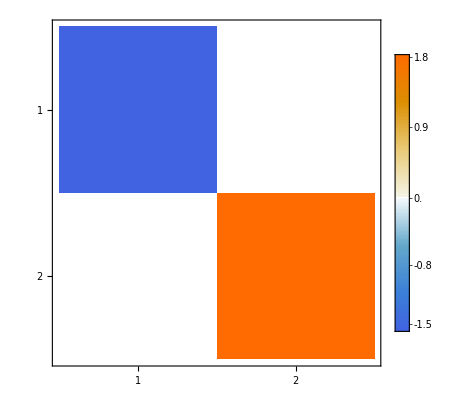

```mathematica
m=2;
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
G=JMat[A];
GAGt=G.A.Gᵀ;
Map[MatrixForm,{G.Gᵀ,GAGt}];
MatrixPlot[Chop[GAGt],PlotLegends->Automatic]
```

To use this in a larger matrix we target a specific entry {i,j} and embed the appropriate tiny rotation in the identity matrix.

```mathematica
SetAttributes[BigJ,HoldFirst];
BigJ[A_,{i_,j_}]:=Module[{m=Length[A],G},
G=IdentityMatrix[m];
G⟦{i,j},{i,j}⟧=JMat[A⟦{i,j},{i,j}⟧];
G
]
```

As always test!

```mathematica
m=7;
A=RandomReal[{-1,1},{m,m}]; A= A + Aᵀ;
{i,j}={5,2};
G=BigJ[A,{i,j}];
GAGt=G.A.Gᵀ;
TabView[Map[MatrixPlot,Chop[{GAGt,G,G.Gᵀ,A}]]]
```

1234

So lets try to string a few of these together. It works just the way we expect if we are careful not to overlap!

```mathematica
m=7;
A=A0=RandomReal[{-1,1},{m,m}]; A= A + Aᵀ;
Data=Table[
G=BigJ[A,ij];
A=G.A.Gᵀ,
{ij,{{1,2},{3,4},{5,6}}}];
SetOptions[MatrixPlot, 
ColorRules->{0->Green},Mesh->All,MeshStyle->Red];
TabView[Map[MatrixPlot,Chop[Data]]]
```

123

If we overlap zeros that were made earlier they get messed up.

```mathematica
m=7;
A0=RandomReal[{-1,1},{m,m}]; A0= A0 + A0ᵀ;
A=A0;
Data=Table[
G=BigJ[A,ij];
A=G.A.Gᵀ,
{ij,{{1,2},{1,3},{1,4},{1,5},{1,6},{1,7}}}];
SetOptions[MatrixPlot, ColorRules->{0->Green},Mesh->All,MeshStyle->Red];
TabView[Map[MatrixPlot,Chop[Data]]]
MatrixForm[A]
```

123456

(-1.7948 | -0.492756 | 0.440746 | 0.521403 | -0.362689 | 0.0495347 | 3.00822×10^-17
-0.492756 | 0.854924 | 0.577163 | -1.33747 | 0.519927 | 0.349474 | -0.193195
0.440746 | 0.577163 | 0.405321 | 0.0782387 | 1.52987 | -0.49153 | 0.0781847
0.521403 | -1.33747 | 0.0782387 | -0.541239 | 0.0364811 | -1.25305 | 0.522533
-0.362689 | 0.519927 | 1.52987 | 0.0364811 | 0.431994 | 0.445696 | 1.01881
0.0495347 | 0.349474 | -0.49153 | -1.25305 | 0.445696 | 0.990645 | -0.332373
-1.38778×10^-17 | -0.193195 | 0.0781847 | 0.522533 | 1.01881 | -0.332373 | 0.734139)

Jacobi (or more likely one of his helpers aka computers or computes) was doing this by hand and would have been painstakingly updating a block of numbers.

You would like to be done as fast as possible.

You can do any of the entries.

Which one should you do?

Jacobi’s plan was “Do the big ones first!”  This assumes that arithmetic is slow (it was then) and that it is fast (true for a small matrix) to find the biggest entry.  
https://en.wikipedia.org/wiki/Jacobi_eigenvalue_algorithm

```mathematica
SetAttributes[JacobiStep, HoldFirst]
JacobiStep[A_]:= Module[{AbsA=Abs[UpperTriangularize[A,1]],ij,G},
(* Find the largest non-diagonal entry *)
ij=Position[AbsA,Max[AbsA]]⟦1⟧;
(* Compute the Jacobi/Given rotation zapping the biggest entry *)
G=BigJ[A,ij];
(* Update A in place *)
A=G.A.Gᵀ;
(* No need to return anything! *)
]
```

As always test.

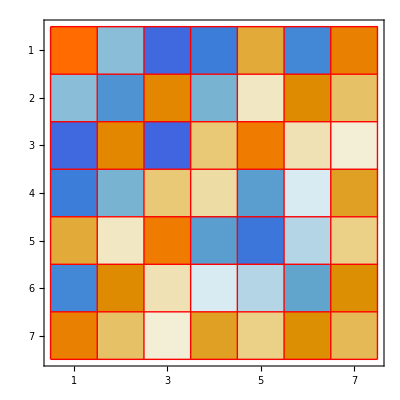
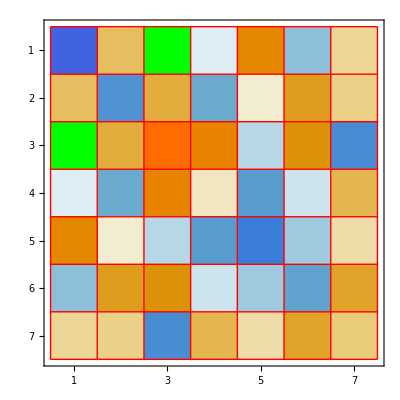

```mathematica
m=7;
A0=RandomReal[{-1,1},{m,m}]; A0= A0 + A0ᵀ;
A=A0;
JacobiStep[A]
Map[MatrixPlot,Chop[{A0,A}]]
```

Now we can do a bunch and know that we are always targeting (and zeroing) large entries! This ensures it always makes progress and that it converges fast at the end!  Of course, copying and pasting is not a good plan! After a few steps the off-diagonal is looking fairly pale!

```mathematica
m=7;
A0=RandomReal[{-1,1},{m,m}]; A0= A0 + A0ᵀ;
A=A0;
TabView[{
JacobiStep[A];MatrixPlot[Chop[A]],
JacobiStep[A];MatrixPlot[Chop[A]],
JacobiStep[A];MatrixPlot[Chop[A]],
JacobiStep[A];MatrixPlot[Chop[A]],
JacobiStep[A];MatrixPlot[Chop[A]],
JacobiStep[A];MatrixPlot[Chop[A]],
JacobiStep[A];MatrixPlot[Chop[A]],
JacobiStep[A];MatrixPlot[Chop[A]]}]
```

12345678

Automation is a good thing!

```mathematica
m=7;
A0=RandomReal[{-1,1},{m,m}]; A0= A0 + A0ᵀ;
A=A0;
MaxIter=16;
TabView[Table[
JacobiStep[A];MatrixPlot[Chop[A]],
{MaxIter}]]
```

12345678910111213141516

#### Demo

Animation is a good thing!

```mathematica
m=7;
A0=RandomReal[{-1,1},{m,m}]; A0= A0 + A0ᵀ;
A=A0;
MaxIter=89;
ListAnimate[Table[
JacobiStep[A];MatrixPlot[Chop[A],PlotLabel->i],
{i,MaxIter}],8]
```

Things to note, something about our choices is pushing the negative eigenvalues up and the positive eigenvalues down!  Other choices will do other things! The common choice is to push the big (either positive or negative eigenvalues up) and the small eigenvalues down!

Like all eigenvalue algorithms this is iterative.  We are always interested in knowing if and how fast iterative algorithms  converge.  One way to measure how far a matrix is from diagonal is to square and then sum all the off-diagonal entries and then take a square root. Doing enough work to touch every entry of the matrix is called a sweep.  In other words, a sweep is “m” steps of the algorithm.

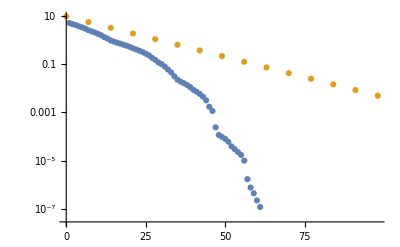

```mathematica
Γ[A_]:=√(Norm[A,"Frobenius"]^2-Norm[Diagonal[A]]^2)

m=7;
A0=RandomReal[{-1,1},{m,m}]; A0= A0 + A0ᵀ;
A=A0;
MaxIter=10^2;
Data=Table[
{i,JacobiStep[A];Γ[A]},
{i,MaxIter}];
C1Data=Table[
{k m,((1-1/m)^(m/2))^(k-1)Γ[A0]},
{k,0, Floor[MaxIter/m]}] ;

ListLogPlot[{Data,C1Data},PlotRange->All,
GridLines->{Range[0,MaxIter,m],Automatic}]
```

It is clear that the algorithm converges significantly faster than the simple bound.  There is a more complicated theorem that says that eventually the convergence is quadratic.  This means that for n big enough there is a k and a c satisfying
	Γ(A_(n+k))≤c (Γ(A_n))^2.
This means the last few steps are very quick. You can see the speed up at the very end.

This algorithm has more parallelism the standard “QR” Francis algorithm you are going to learn.  It has a developed very quaternionic G4 version that block diagonalizes symmetric matrices.  I am working on an alternative G4 and a G8 algorithm that make progress with a simple plan of “move the big entries up” that can work on non-symmetric matrices.

## Bisection

This is an old but useful technique! An m×m symmetric tridiagonal matrix 
	T=(a_1 | b_1 |   |  
b_1 | a_2 | b_2 |  
  | b_2 | a_3 | ⋱
  |   | ⋱ | ⋱)
is irreducible if b_i≠0 for any i.   If some b_i=0 we can split A into smaller non-interacting sub matrices!  Bisection provides a fast way to localize eigenvalues in an interval.

### Sturm Sequence

Look at the pattern for the eigenvalues of the top k×k submatrix A^(k)=A⟦1;;k,1;;k⟧.

```mathematica
m=5;{a,b}={RandomReal[{-1,1},m],RandomReal[{-1,1},m-1]};
A=SparseArray[{Band[{1,1}]->a,Band[{1,2}]->b,Band[{2,1}]->b},{m,m}];
TableForm[Table[
{Framed[λs=Sort[Eigenvalues[A⟦1;;k,1;;k⟧]]],Apply[Times,λs]},
{k,1,m}],
TableHeadings->{Automatic,{"λs","det"}},TableAlignments->Center
]
```

| λs | det
1 | {0.637557} | 0.637557
2 | {-0.276708,1.15234} | -0.318862
3 | {-0.733835,-0.157647,1.17029} | 0.135387
4 | {-1.05866,-0.227463,1.02587,1.20791} | 0.298395
5 | {-1.22831,-0.386142,-0.107836,1.16229,1.63338} | -0.0971003

The eigenvalues interlace in the sense that λ_j^(k+1)<λ_j^(k)<λ_(j+1)^(k+1) where λ_j^k is the j^theigenvalue of the top k×k submatrix.  This property is called “interlacing”.  It is actually true for all real symmetric matrices but we only need it for tridiagonal!

#### Det[A^(k)]=λ_1^(k)λ_2^(k)(…λ)_k^(k)

Computing det(A^(k)) is cheap since det(A^(k))=a_k det(A^(k-1))-b_(k-1)^2 det(A^(k-2)).  We actually want p^(k)(x)=det(A^(k)-x Id) which is simply
	p^(k)(x)=(a_k-x)p^(k-1)(x)-b_(k-1)^2 p^(k-2)(x) with p^(-1)(x)=0 and p^(0)(x)=1.
The “Sturm Sequence” p^(0)(x),p^(1)(x),…,p^(m)(x) can be computed cheaply.  It is not obvious, but this trick can count eigenvalues in intervals! Start with x=0 and remember the determinant is the product of the eigenvalues.

```mathematica
Clear[p,k,x]
p[{a_,b_},-1,x_]=0;
p[{a_,b_},0,x_]=1;
p[{a_,b_},1,x_]:=p[{a,b},1,x]=(a⟦1⟧-x)
p[{a_,b_},k_,x_]:=p[{a,b},k,x]=(a⟦k⟧-x)p[{a,b},k-1,x]-b⟦k-1⟧^2 p[{a,b},k-2,x]
sturm=Table[p[{a,b},k,0],{k,0,m}]
TableForm[{Sign[sturm]},TableHeadings->{{"Sturm-Sign"},Table[k,{k,0,m}]}]
```

{1,0.637557,-0.318862,0.135387,0.298395,-0.0971003}

| 0 | 1 | 2 | 3 | 4 | 5
Sturm-Sign | 1 | 1 | -1 | 1 | 1 | -1

```mathematica
Sort[Eigenvalues[A]]
```

{-2.22716,-1.39283,-0.254829,0.613438,0.95827}

Every time the minors grow a new negative eigenvalue the sign of the determinant flips. Counting the flips counts how many negative eigenvalues there are!  Lets see it on a slightly larger matrix

```mathematica
Clear[p,k,x,SturmSigns]
m=12;
{a,b}=Map[RandomReal[{-1,1},#]&,{m,m-1}];
T=SparseArray[{Band[{1,1}]->a,Band[{1,2}]->b,Band[{2,1}]->b},{m,m}];
p[{a_,b_},-1,x_]=0;
p[{a_,b_},0,x_]=1;
p[{a_,b_},1,x_]:=p[{a,b},1,x]=(a⟦1⟧-x)
p[{a_,b_},k_,x_]:=p[{a,b},k,x]=(a⟦k⟧-x)p[{a,b},k-1,x]-b⟦k-1⟧^2 p[{a,b},k-2,x]
SturmSigns[x_]:=Sign[Table[p[{a,b},k,x],{k,0,m}]];
TableForm[{SturmSigns[0]},TableHeadings->{{"SturmSigns[0]"},Table[k,{k,0,m}]}]
λs=Sort[Eigenvalues[T]]
```

| 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
SturmSigns[0] | 1 | -1 | -1 | -1 | 1 | -1 | -1 | 1 | 1 | 1 | -1 | -1 | 1

{-1.4654,-0.980639,-0.892416,-0.649803,-0.554227,-0.102646,0.0863486,0.152572,0.329049,0.539613,0.669163,0.880931}

You can automate counting the sign changes and negative eigenvalues lots of different ways

```mathematica
SturmSigns[0]
Split[SturmSigns[0]]
{Length[Split[SturmSigns[0]]]-1,Count[Sign[Eigenvalues[T]],-1]}
```

{1,1,-1,-1,1,1,-1,1,1,-1,-1,1,-1}

{{1,1},{-1,-1},{1,1},{-1},{1,1},{-1,-1},{1},{-1}}

{7,7}

### Eigenvalues in (x_0,x_1)

The shift x lets you count the number of eigenvalues less than any number.  We just did x=0 as a warm up!  We can count the eigenvalues in any interval (x_0,x_1).  It is pretty simple

```mathematica
Clear[p,k,x,SturmSigns]
m=12;
{a,b}=Map[RandomReal[{-1,1},#]&,{m,m-1}];
T=SparseArray[{Band[{1,1}]->a,Band[{1,2}]->b,Band[{2,1}]->b},{m,m}];
p[{a_,b_},-1,x_]=0;
p[{a_,b_},0,x_]=1;
p[{a_,b_},1,x_]:=p[{a,b},1,x]=(a⟦1⟧-x)
p[{a_,b_},k_,x_]:=p[{a,b},k,x]=(a⟦k⟧-x)p[{a,b},k-1,x]-b⟦k-1⟧^2 p[{a,b},k-2,x]
SturmSigns[x_]:=Sign[Table[p[{a,b},k,x],{k,0,m}]];

{x0,x1}={-0.2,1.1};
Map[ (Length[Split[SturmSigns[#]]]-1)&,{x0,x1}]
λs=Sort[Eigenvalues[T]]
Select[λs,(x0≤#≤x1)&]
```

{6,11}

{-2.1606,-1.50478,-1.47181,-1.24011,-0.924815,-0.637732,-0.0441958,0.298986,0.308862,0.847312,0.909929,1.13761}

{-0.0441958,0.298986,0.308862,0.847312,0.909929}

If you want all the eigenvalues in an interval and there are 20 processors available split the original interval into 19 sub intervals and count (in parallel) how many eigenvalues are less than each of the 20 split points!

Throw away intervals with no eigenvalues.

Further subdivide intervals with eigenvalues.

Repeat until you have a bunch of intervals with a single eigenvalue.

If you need better resolution of each eigenvalue continue splitting intervals.

## Divide and Conquer

This is a new (introduced in 1981 AAS was in university) and developing technique. The idea is to recursively split matrices into smaller matrices.  We are looking at a symmetric tridiagonal matrices T from symmetric Hessenberg reductions.

An m×m symmetric tridiagonal matrix 
	T=(a_1 | b_1 |   |  
b_1 | a_2 | b_2 |  
  | b_2 | a_3 | ⋱
  |   | ⋱ | ⋱)
is irreducible if b_i≠0 for any i. Divide and conquer splits matrices by finding Q so that 
	Q.T.Qᵀ=(T_top | 0
0 | T_bot).
Splitting the matrix involves accurately solving a nonlinear equation of a very specific form.

### Splitting the Problem

Divide and conquer recursively splits a tridiagonal matrix into smaller tridiagonal matrices coupled with a rank one matrix.  An example will clarify some of this

```mathematica
SetOptions[MatrixPlot, Mesh->All,PlotLegends->Automatic];
s=4;m=2 s;{a,b}={RandomReal[{-1,1},m],RandomReal[{-1,1},m-1]};
T=SparseArray[{Band[{1,1}]->a,Band[{1,2}]->b,Band[{2,1}]->b},{m,m}];
{T1,T2}={T1Hat,T2Hat}={T⟦1;;4,1;;4⟧,T⟦5;;8,5;;8⟧};
β=T⟦s+1,s⟧;T1Hat⟦-1,-1⟧-=β; T2Hat⟦1,1⟧-=β;
THat= ArrayFlatten[({{T1Hat, 0}, {0, T2Hat}})];
vec =SparseArray[{s->1,s+1->1},m];
ROne=β KroneckerProduct[vec,vec];
TabView[{
"T"->MatrixPlot[T],
"THat"->MatrixPlot[THat],
"ROne"->MatrixPlot[ROne],
"THat+ROne"->MatrixPlot[THat+ROne]}]
```

1234

Compute the eigen decomposition of the smaller matrices
	(T̂)_1=Q_1.D_1.Q_1^ᵀ  and (T̂)_2=Q_2.D_2.Q_2^ᵀ
then if z=(Q_1⟦-1⟧ | Q_2⟦1⟧) i.e the first row of Q_2 appended to the last row of Q_2then
	T=(Q_1 |  
  | Q_2).((D_1 |  
  | D_2)+β z⊗z).(Q_1^ᵀ |  
  | Q_2^ᵀ)	
This means we can focus on the inside matrix which is diagonal plus rank one

```mathematica
s=4;m=2 s;{a,b}={RandomReal[{-1,1},m],RandomReal[{-1,1},m-1]};
T=SparseArray[{Band[{1,1}]->a,Band[{1,2}]->b,Band[{2,1}]->b},{m,m}];
{T1,T2}={T1Hat,T2Hat}={T⟦1;;4,1;;4⟧,T⟦5;;8,5;;8⟧};
β=T⟦s+1,s⟧;T1Hat⟦-1,-1⟧-=β; T2Hat⟦1,1⟧-=β;
{{λ1,Q1},{λ2,Q2}}=Map[Eigensystem,{T1Hat,T2Hat}];{Q1,Q2}=Map[Transpose,{Q1,Q2}];
z=Join[Q1⟦-1⟧,Q2⟦1⟧];
BigQ=ArrayFlatten[({{Q1, 0}, {0, Q2}})];
InsideMat = SparseArray[Band[{1,1}]->Join[λ1,λ2],{m,m}]+β KroneckerProduct[z,z];
Norm[T-BigQ.InsideMat.BigQᵀ]
```

2.61464×10^-15

If we can solve the very-very-very special inside eigenvalue problems we can recursively split our original problem.

#### Eigen values of Diagonal Plus Symmetric Rank One D+ω⊗ω

Claim: The eigenvalues of D+ω⊗ω are the roots of secular equation
	f(λ)=1+∑_(j=1)^m (ω_j)^2/(d_j-λ)=0
Argument: (D+ω⊗ω).v=λ v means 
	(D-λ Id).v=-ω (ω.v)
or equivalently 
	v+(D-λ Id)^-1 ω (ω.v)=0.
Dot this with ω to get
	ω.v+ω.(D-λ Id)^-1.ω (ω.v)=0
then factor out ω.v to get
	(ω.v)(1+ω.(D-λ Id)^-1.ω )=0
and cancel to get the secular equation
	(1+ω.(D-λ Id)^-1.ω )=0.
Or in other words
	(D-λ Id)^-1=(D_11-λ | 0 | 0 |   |  
0 | D_22-λ | 0 |   |  
0 | 0 | D_33-λ |   |  
  |   |   |   |  )^-1
or in other words
	(D-λ Id)^-1=(1/(D_11-λ) | 0 | 0 |   |  
0 | 1/(D_22-λ) | 0 |   |  
0 | 0 | 1/(D_33-λ) |   |  
  |   |   |   |  )
so 
  1+ω.(D-λ Id)^-1.ω =1+∑_(i=1)^n ω_i^2/(D_ii-λ)=0

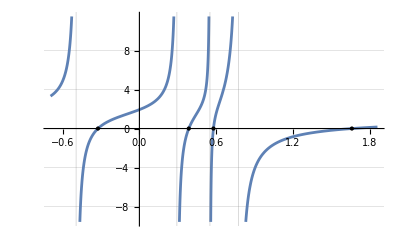

```mathematica
Clear[λ]
m=4;
{d,w}=RandomReal[{-1,1},{2,m}];
A=SparseArray[Band[{1,1}]->d,{m,m}]+KroneckerProduct[w,w];
f[λ_]:= 1+Sum[w⟦j⟧^2/(d⟦j⟧-λ),{j,1,m}];
λs=Sort[Eigenvalues[A]];
ϵ=0.2;
{a,b}={Min[Join[d,λs]],Max[Join[d,λs]]}+ϵ {-1,1};
Plot[f[λ],{λ,a,b},
Epilog->Map[Point[{#,0}]&,λs],
Exclusions->d,
GridLines->{d,Automatic}]
```

The secular equation can be solved very efficiently (using specialized variants of Newton’s Method) because of its special structure!

## Summary

There are 3 other practical dense symmetric eigenvalue algorithms!  All are used in  the real world! All have easily available quality implementations.

Jacobi:

Used to resolve small eigenvalues accurately.

Used on hardware without fully implemented math libraries.

Bisection:

Used when only a subset of eigenvalues are needed

Used to isolate eigenvalues.

Divide and Conquer:

Much newer and still evolving.

Similar operation count as QR for eigenvalues

Lower operation count as QR for eigenvectors.

Frequently deflates rapidly and beats the typical operation counts.